```mathematica
(*Mathematica*)
```

```mathematica
Clear[f,g,mu,s]
```

```mathematica
(*Kleinian 2 group   2Apollonian Disk*)
```

```mathematica
s[1]={{1+I,1},{1,1-I}}
s[2]={{1,0},{-2*I,1}}
s[3]=Inverse[s[1]]
s[4]=Inverse[s[2]]
```

{{1+ⅈ,1},{1,1-ⅈ}}

{{1,0},{-2 ⅈ,1}}

{{1-ⅈ,-1},{-1,1+ⅈ}}

{{1,0},{2 ⅈ,1}}

```mathematica
f[z_,i_]:=(s[i][[1,1]]*z+s[i][[1,2]])/(s[i][[2,1]]*z+s[i][[2,2]])
```

```mathematica
(*doubled 2 Apollonian 16 elements*)
```

```mathematica
w=Flatten[Table[ExpandAll[f[f[z,i],j]],{i,4},{j,4}]]
```

{1/((1-ⅈ)+1/((1-ⅈ)+z)+((1+ⅈ) z)/((1-ⅈ)+z))+(1+ⅈ)/(((1-ⅈ)+z) ((1-ⅈ)+1/((1-ⅈ)+z)+((1+ⅈ) z)/((1-ⅈ)+z)))+(2 ⅈ z)/(((1-ⅈ)+z) ((1-ⅈ)+1/((1-ⅈ)+z)+((1+ⅈ) z)/((1-ⅈ)+z))),1/((1-ⅈ)+z-(2+2 ⅈ)/((1-ⅈ)+z)-(6 ⅈ z)/((1-ⅈ)+z)+((2-2 ⅈ) z^2)/((1-ⅈ)+z))+((1+ⅈ) z)/((1-ⅈ)+z-(2+2 ⅈ)/((1-ⅈ)+z)-(6 ⅈ z)/((1-ⅈ)+z)+((2-2 ⅈ) z^2)/((1-ⅈ)+z)),-1/((1+ⅈ)-1/((1-ⅈ)+z)-((1+ⅈ) z)/((1-ⅈ)+z))+(1-ⅈ)/(((1-ⅈ)+z) ((1+ⅈ)-1/((1-ⅈ)+z)-((1+ⅈ) z)/((1-ⅈ)+z)))+(2 z)/(((1-ⅈ)+z) ((1+ⅈ)-1/((1-ⅈ)+z)-((1+ⅈ) z)/((1-ⅈ)+z))),1/((1-ⅈ)+z+(2+2 ⅈ)/((1-ⅈ)+z)+(6 ⅈ z)/((1-ⅈ)+z)-((2-2 ⅈ) z^2)/((1-ⅈ)+z))+((1+ⅈ) z)/((1-ⅈ)+z+(2+2 ⅈ)/((1-ⅈ)+z)+(6 ⅈ z)/((1-ⅈ)+z)-((2-2 ⅈ) z^2)/((1-ⅈ)+z)),1/((1-ⅈ)+z/(1-2 ⅈ z))+((1+ⅈ) z)/((1-2 ⅈ z) ((1-ⅈ)+z/(1-2 ⅈ z))),z/(1-2 ⅈ z-(2 ⅈ z)/(1-2 ⅈ z)-(4 z^2)/(1-2 ⅈ z)),-1/((1+ⅈ)-z/(1-2 ⅈ z))+((1-ⅈ) z)/((1-2 ⅈ z) ((1+ⅈ)-z/(1-2 ⅈ z))),z/(1-2 ⅈ z+(2 ⅈ z)/(1-2 ⅈ z)+(4 z^2)/(1-2 ⅈ z)),1/((1-ⅈ)-1/((1+ⅈ)-z)+((1-ⅈ) z)/((1+ⅈ)-z))-(1+ⅈ)/(((1+ⅈ)-z) ((1-ⅈ)-1/((1+ⅈ)-z)+((1-ⅈ) z)/((1+ⅈ)-z)))+(2 z)/(((1+ⅈ)-z) ((1-ⅈ)-1/((1+ⅈ)-z)+((1-ⅈ) z)/((1+ⅈ)-z))),-1/((1+ⅈ)-(2-2 ⅈ)/((1+ⅈ)-z)-z-(6 ⅈ z)/((1+ⅈ)-z)+((2+2 ⅈ) z^2)/((1+ⅈ)-z))+((1-ⅈ) z)/((1+ⅈ)-(2-2 ⅈ)/((1+ⅈ)-z)-z-(6 ⅈ z)/((1+ⅈ)-z)+((2+2 ⅈ) z^2)/((1+ⅈ)-z)),-1/((1+ⅈ)+1/((1+ⅈ)-z)-((1-ⅈ) z)/((1+ⅈ)-z))-(1-ⅈ)/(((1+ⅈ)-z) ((1+ⅈ)+1/((1+ⅈ)-z)-((1-ⅈ) z)/((1+ⅈ)-z)))-(2 ⅈ z)/(((1+ⅈ)-z) ((1+ⅈ)+1/((1+ⅈ)-z)-((1-ⅈ) z)/((1+ⅈ)-z))),-1/((1+ⅈ)+(2-2 ⅈ)/((1+ⅈ)-z)-z+(6 ⅈ z)/((1+ⅈ)-z)-((2+2 ⅈ) z^2)/((1+ⅈ)-z))+((1-ⅈ) z)/((1+ⅈ)+(2-2 ⅈ)/((1+ⅈ)-z)-z+(6 ⅈ z)/((1+ⅈ)-z)-((2+2 ⅈ) z^2)/((1+ⅈ)-z)),1/((1-ⅈ)+z/(1+2 ⅈ z))+((1+ⅈ) z)/((1+2 ⅈ z) ((1-ⅈ)+z/(1+2 ⅈ z))),z/(1+2 ⅈ z-(2 ⅈ z)/(1+2 ⅈ z)+(4 z^2)/(1+2 ⅈ z)),-1/((1+ⅈ)-z/(1+2 ⅈ z))+((1-ⅈ) z)/((1+2 ⅈ z) ((1+ⅈ)-z/(1+2 ⅈ z))),z/(1+2 ⅈ z+(2 ⅈ z)/(1+2 ⅈ z)-(4 z^2)/(1+2 ⅈ z))}

```mathematica
(*Molien function of 16 product group*)
```

```mathematica
g[z_]=Together[Sum[1/w[[i]],{i,16}]]//Chop
```

(8 (3+19 ⅈ z-34 z^2+4 ⅈ z^3-15 z^4+81 ⅈ z^5-150 z^6+74 ⅈ z^7-300 z^8-200 ⅈ z^9))/(z (-1+(1+ⅈ) z) (-ⅈ+(1+ⅈ) z) (ⅈ+(1+ⅈ) z) (1+(1+ⅈ) z) (2+(1+2 ⅈ) z) (1+(1+3 ⅈ) z) (-2 ⅈ+(2+ⅈ) z) (-ⅈ+(3+ⅈ) z))

```mathematica
z/.NSolve[Numerator[g[z]]==0,z]
```

{-0.562568+0.477469 ⅈ,-0.47522-0.428329 ⅈ,-0.411546+0.803744 ⅈ,-0.102404+0.302297 ⅈ,0.-0.810362 ⅈ,0.102404+0.302297 ⅈ,0.411546+0.803744 ⅈ,0.47522-0.428329 ⅈ,0.562568+0.477469 ⅈ}

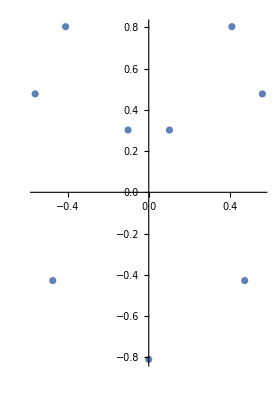

```mathematica
ComplexListPlot[%]
```

```mathematica
z/.NSolve[Denominator[g[z]]==0,z]
```

{-0.5-0.5 ⅈ,-0.5+0.5 ⅈ,-0.4+0.8 ⅈ,-0.1+0.3 ⅈ,0.,0.1+0.3 ⅈ,0.4+0.8 ⅈ,0.5-0.5 ⅈ,0.5+0.5 ⅈ}

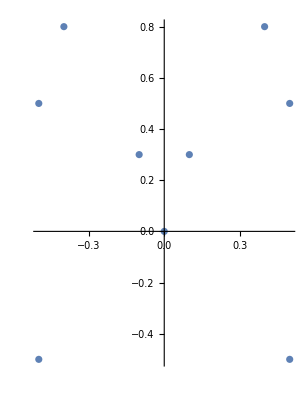

```mathematica
ComplexListPlot[%]
```

```mathematica
g0=ComplexPlot[g[x],{x,-4-I*4,4+I*4},ColorFunction->"CyclicReImLogAbs",PlotPoints->50,ImageSize->Full];
```

```mathematica
(*g0=JuliaSetPlot[f[z],z,ColorFunction->"CMYKColors",ImageResolution->2000,ImageSize->2000]*)
```

#### 3D Mandelbrot

```mathematica
(*Julia with SQRT(x^2+y^2) limited measure*)
(*by R. L. BAGULA 17 Apr 2023 © *)
numberOfz2ToEscape[z_] := Block[
	{escapeCount, nz = N[z],nzold=0},
	For[
		escapeCount = 0,
		(Sqrt[Re[nz]^2+Im[nz]^2] <128) && (escapeCount <2048) && (Abs[nz-nzold]>10^(-3)),
		nzold=nz;
		nz=g[nz]*nz^2/3.125;
		++escapeCount
	];
	escapeCount*If[(Abs[nz-nzold]>10^(-3))||escapeCount>1000,escapeCount*Abs[Arg[nz]],escapeCount*Abs[ArcTan[nz]+I*ArcTan[nz]*Tan[1]-Arg[z]]]
]
```

```mathematica
FractalPure[m_][{{ReMin_, ReMax_, ReSteps_},
			 {ImMin_, ImMax_, ImSteps_}}] :=
		ParallelTable[
			numberOfz2ToEscape[x + y I],
			{y, ImMin, ImMax, (ImMax - ImMin)/ImSteps},
			{x, ReMin, ReMax, (ReMax - ReMin)/ReSteps}
		
	]
```

```mathematica
arraym=FractalPure[m][{{-1.2501+0.125,1.25-0.125,1000},{-1.5+0.125,1.0-0.125,1000}}];
```

```mathematica
g1=ListPlot3D[Abs[Log[1/Max[arraym]+arraym]], Mesh -> False,AspectRatio -> Automatic,Boxed->False, Axes->False,ColorFunction->"CMYKColors",Background->Black,ViewPoint->Above,ImageSize->2000];
```

```mathematica
g2=ListDensityPlot[Log[Abs[1/Max[arraym]+arraym-512/(arraym+Max[arraym])]],
                          Mesh -> False,
		                  AspectRatio -> Automatic,
		                 ColorFunction->"GreenPinkTones",ImageSize->2000,Frame->False];
```

```mathematica
colortab=Reverse[Union[{{0,0,0.1875},{0,0,0.20833333333333331},{0,0,0.22916666666666666},{0,0,0.25},{0,0,0.2708333333333333},{0,0,0.28125},{0,0,0.29166666666666663},{0,0,0.3125},{0,0,1/3},{0,0,0.34375},{0,0,0.375},{0,0,0.40625},{0,0,0.4375},{0,0,0.46875},{0,0,1/2},{0,0,0.5625},{0,0,0.625},{0,0,0.6875},{0,0,0.75},{0,0,0.8125},{0,0,0.875},{0,0,0.9375},{0,0,1},{0,0.020833333333333332,1/3},{0,0.03125,1/2},{0,0.041666666666666664,1/3},{0,0.0625,1/3},{0,0.0625,1/2},{0,0.0625,1},{0,0.08333333333333333,1/3},{0,0.09375,1/2},{0,0.10416666666666666,1/3},{0,0.125,1/3},{0,0.125,1/2},{0,0.125,1},{0,0.14583333333333331,1/3},{0,0.15625,1/2},{0,0.16666666666666666,1/3},{0,0.1875,1/3},{0,0.1875,1/2},{0,0.1875,1},{0,0.20833333333333331,1/3},{0,0.21875,1/2},{0,0.22916666666666666,1/3},{0,0.25,1/3},{0,0.25,1/2},{0,0.25,1},{0,0.2708333333333333,1/3},{0,0.28125,1/2},{0,0.29166666666666663,1/3},{0,0.3125,1/3},{0,0.3125,1/2},{0,0.3125,1},{0,1/3,1/3},{0,0.34375,1/2},{0,0.375,1/2},{0,0.375,1},{0,0.40625,1/2},{0,0.4375,1/2},{0,0.4375,1},{0,0.46875,1/2},{0,0.5,1},{0,1/2,1/2},{0,0.5625,1},{0,0.625,1},{0,0.6875,1},{0,0.75,1},{0,0.8125,1},{0,0.875,1},{0,0.9375,1},{0,1,1},{0.,0.,0.375},{0.,0.,0.41666666666666663},{0.,0.,0.4583333333333333},{0.,0.,0.5},{0.,0.,0.5416666666666666},{0.,0.,0.5833333333333333},{0.,0.,0.625},{0.,0.,0.6666666666666666},{0.,0.041666666666666664,0.6666666666666666},{0.,0.08333333333333333,0.6666666666666666},{0.,0.125,0.6666666666666666},{0.,0.16666666666666666,0.6666666666666666},{0.,0.20833333333333331,0.6666666666666666},{0.,0.25,0.6666666666666666},{0.,0.29166666666666663,0.6666666666666666},{0.,0.3333333333333333,0.6666666666666666},{0.,0.375,0.6666666666666666},{0.,0.41666666666666663,0.6666666666666666},{0.,0.4583333333333333,0.6666666666666666},{0.,0.5,0.6666666666666666},{0.,0.5416666666666666,0.6666666666666666},{0.,0.5833333333333333,0.6666666666666666},{0.,0.625,0.6666666666666666},{0.,0.6666666666666666,0.6666666666666666},{0.020833333333333332,1/3,1/3},{0.03125,1/2,1/2},{0.041666666666666664,1/3,0.3125},{0.041666666666666664,0.6666666666666666,0.6666666666666666},{0.0625,1/3,0.29166666666666663},{0.0625,1/2,0.46875},{0.0625,1,1},{0.08333333333333333,1/3,0.2708333333333333},{0.08333333333333333,0.6666666666666666,0.625},{0.09375,1/2,0.4375},{0.10416666666666666,1/3,0.25},{0.125,1/3,0.22916666666666666},{0.125,1/2,0.40625},{0.125,0.6666666666666666,0.5833333333333333},{0.125,1,0.9375},{0.14583333333333331,1/3,0.20833333333333331},{0.15625,1/2,0.375},{0.16666666666666666,1/3,0.1875},{0.16666666666666666,0.6666666666666666,0.5416666666666666},{0.1875,0,0},{0.1875,1/3,0.16666666666666666},{0.1875,1/2,0.34375},{0.1875,1,0.875},{0.20833333333333331,0,0},{0.20833333333333331,1/3,0.14583333333333331},{0.20833333333333331,0.6666666666666666,0.5},{0.21875,1/2,0.3125},{0.22916666666666666,0,0},{0.22916666666666666,1/3,0.125},{0.25,0,0},{0.25,1/3,0.10416666666666666},{0.25,1/2,0.28125},{0.25,0.6666666666666666,0.4583333333333333},{0.25,1,0.8125},{0.2708333333333333,0,0},{0.2708333333333333,1/3,0.08333333333333333},{0.28125,0,0},{0.28125,1/2,0.25},{0.29166666666666663,0,0},{0.29166666666666663,1/3,0.0625},{0.29166666666666663,0.6666666666666666,0.41666666666666663},{0.3125,0,0},{0.3125,1/3,0.041666666666666664},{0.3125,1/2,0.21875},{0.3125,1,0.75},{0.3333333333333333,0.6666666666666666,0.375},{1/3,0,0},{1/3,0.020833333333333332,0},{1/3,0.041666666666666664,0},{1/3,0.0625,0},{1/3,0.08333333333333333,0},{1/3,0.10416666666666666,0},{1/3,0.125,0},{1/3,0.14583333333333331,0},{1/3,0.16666666666666666,0},{1/3,0.1875,0},{1/3,0.20833333333333331,0},{1/3,0.22916666666666666,0},{1/3,0.25,0},{1/3,0.2708333333333333,0},{1/3,0.29166666666666663,0},{1/3,0.3125,0},{1/3,1/3,0},{1/3,1/3,0.020833333333333332},{0.34375,0,0},{0.34375,1/2,0.1875},{0.375,0,0},{0.375,0.,0.},{0.375,1/2,0.15625},{0.375,0.6666666666666666,0.3333333333333333},{0.375,1,0.6875},{0.40625,0,0},{0.40625,1/2,0.125},{0.41666666666666663,0.,0.},{0.41666666666666663,0.6666666666666666,0.29166666666666663},{0.4375,0,0},{0.4375,1/2,0.09375},{0.4375,1,0.625},{0.4583333333333333,0.,0.},{0.4583333333333333,0.6666666666666666,0.25},{0.46875,0,0},{0.46875,1/2,0.0625},{0.5,0.,0.},{0.5,0.6666666666666666,0.20833333333333331},{0.5,1,0.5625},{1/2,0,0},{1/2,0.03125,0},{1/2,0.0625,0},{1/2,0.09375,0},{1/2,0.125,0},{1/2,0.15625,0},{1/2,0.1875,0},{1/2,0.21875,0},{1/2,0.25,0},{1/2,0.28125,0},{1/2,0.3125,0},{1/2,0.34375,0},{1/2,0.375,0},{1/2,0.40625,0},{1/2,0.4375,0},{1/2,0.46875,0},{1/2,1/2,0},{1/2,1/2,0.03125},{0.5416666666666666,0.,0.},{0.5416666666666666,0.6666666666666666,0.16666666666666666},{0.5625,0,0},{0.5625,1,0.5},{0.5833333333333333,0.,0.},{0.5833333333333333,0.6666666666666666,0.125},{0.625,0,0},{0.625,0.,0.},{0.625,0.6666666666666666,0.08333333333333333},{0.625,1,0.4375},{0.6666666666666666,0.,0.},{0.6666666666666666,0.041666666666666664,0.},{0.6666666666666666,0.08333333333333333,0.},{0.6666666666666666,0.125,0.},{0.6666666666666666,0.16666666666666666,0.},{0.6666666666666666,0.20833333333333331,0.},{0.6666666666666666,0.25,0.},{0.6666666666666666,0.29166666666666663,0.},{0.6666666666666666,0.3333333333333333,0.},{0.6666666666666666,0.375,0.},{0.6666666666666666,0.41666666666666663,0.},{0.6666666666666666,0.4583333333333333,0.},{0.6666666666666666,0.5,0.},{0.6666666666666666,0.5416666666666666,0.},{0.6666666666666666,0.5833333333333333,0.},{0.6666666666666666,0.625,0.},{0.6666666666666666,0.6666666666666666,0.},{0.6666666666666666,0.6666666666666666,0.041666666666666664},{0.6875,0,0},{0.6875,1,0.375},{0.75,0,0},{0.75,1,0.3125},{0.8125,0,0},{0.8125,1,0.25},{0.875,0,0},{0.875,1,0.1875},{0.9375,0,0},{0.9375,1,0.125},{1,0,0},{1,0,1},{1,1/100,81/100},{1,1/100,1},{1,1/25,16/25},{1,1/25,81/100},{1,1/25,1},{1,0.0625,0},{1,9/100,49/100},{1,9/100,16/25},{1,9/100,81/100},{1,9/100,1},{1,0.125,0},{1,4/25,9/25},{1,4/25,49/100},{1,4/25,16/25},{1,4/25,81/100},{1,4/25,1},{1,0.1875,0},{1,0.25,0},{1,1/4,1/4},{1,1/4,9/25},{1,1/4,49/100},{1,1/4,16/25},{1,1/4,81/100},{1,1/4,1},{1,0.3125,0},{1,9/25,4/25},{1,9/25,1/4},{1,9/25,9/25},{1,9/25,49/100},{1,9/25,16/25},{1,9/25,81/100},{1,9/25,1},{1,0.375,0},{1,0.4375,0},{1,49/100,9/100},{1,49/100,4/25},{1,49/100,1/4},{1,49/100,9/25},{1,49/100,49/100},{1,49/100,16/25},{1,49/100,81/100},{1,49/100,1},{1,0.5,0},{1,0.5625,0},{1,0.625,0},{1,16/25,1/25},{1,16/25,9/100},{1,16/25,4/25},{1,16/25,1/4},{1,16/25,9/25},{1,16/25,49/100},{1,16/25,16/25},{1,16/25,81/100},{1,16/25,1},{1,0.6875,0},{1,0.75,0},{1,81/100,1/100},{1,81/100,1/25},{1,81/100,9/100},{1,81/100,4/25},{1,81/100,1/4},{1,81/100,9/25},{1,81/100,49/100},{1,81/100,16/25},{1,81/100,81/100},{1,81/100,1},{1,0.8125,0},{1,0.875,0},{1,0.9375,0},{1,1,0},{1,1,1/100},{1,1,1/25},{1,1,0.0625},{1,1,9/100},{1,1,4/25},{1,1,1/4},{1,1,9/25},{1,1,49/100},{1,1,16/25},{1,1,81/100},{1,1,1}}]];
```

```mathematica
Length[%]
```

319

```mathematica
cf[l_]:=Block[{niv,rgb},niv=If[l<1/319,1,Ceiling[319*l]];
rgb=colortab[[niv]];
RGBColor[rgb[[1]],rgb[[2]],rgb[[3]]]];
```

```mathematica
g3=ListDensityPlot[Abs[Log[1/Max[arraym]+arraym]], Mesh -> False, AspectRatio -> Automatic, ColorFunction->cf,ImageSize->2000,Frame->False];
```

```mathematica
g4=Rasterize[ListDensityPlot[Log[Abs[1/Max[arraym]+arraym-512/(arraym+Max[arraym])]],
                          Mesh -> False,
		                  AspectRatio -> Automatic,
		                 ColorFunction-> (Hue[3*#]&),ImageSize->2000,Frame->False],RasterSize->2000,ImageSize->2000];
```

```mathematica
Export["j_1000_Herman_rings_Molien_double_product_2Apollonian_rt_Out.10In_monitor.jpg",{g0,g1,g2,g3,g4}]
(*end*)
```

j_1000_Herman_rings_Molien_double_product_2Apollonian_rt_Out.10In_monitor.jpg

Lookup::invrl: The argument Missing[NotAvailable] is not a valid Association or a list of rules.